```mathematica
-Δ*Sqrt[1 - T * Sin[(t)/2]^2]
```

-Δ √(1-T Sin[t/2]^2)

```mathematica
Collect[FullSimplify[FourierCosSeries[Sqrt[1 - T * Sin[(t)/2]^2],t,3]],{Cos[t],Cos[2t],Cos[3t]}]
```

(2 EllipticE[T])/π+(Cos[2 t] (-28 T (16+(-16+T) T) EllipticE[T]+224 (-2+T) (-1+T) T EllipticK[T]))/(105 π T^3)+(Cos[t] (-140 (-2+T) T^2 EllipticE[T]+280 (-1+T) T^2 EllipticK[T]))/(105 π T^3)+1/(105 π T^3)Cos[3 t] (-4 (-2+T) (128+T (-128+3 T)) EllipticE[T]+8 (-1+T) (128+T (-128+27 T)) EllipticK[T])

```mathematica
(-140 (-2+T) T^2 EllipticE[T]+280 (-1+T) T^2 EllipticK[T])/(105 π T^3)//FullSimplify
```

(-4 (-2+T) EllipticE[T]+8 (-1+T) EllipticK[T])/(3 π T)

```mathematica
Series[(4 (2-T) EllipticE[T]+8 (T-1) EllipticK[T])/(3 π T),{T,0,2}]
```

T/4+T^2/16+O[T]^3

```mathematica
Refine[Series[(4 (2-T) EllipticE[T]+8 (T-1) EllipticK[T])/(3 π T),{T,1,2}],Assumptions->T ∈Reals]
```

Floor[-Arg[-1+T]/(2 π)] (2/3 ⅈ (T-1)-19/12 ⅈ (T-1)^2+O[T-1]^3)+Floor[-Arg[-1+T]/(2 π)] (-8/3 ⅈ (T-1)+10/3 ⅈ (T-1)^2+O[T-1]^3)+(4/(3 π)-(ⅈ (-7 ⅈ+3 π+12 ⅈ Log[2]-3 ⅈ Log[-1+T]) (T-1))/(3 π)+(ⅈ (-115 ⅈ+42 π+168 ⅈ Log[2]-42 ⅈ Log[-1+T]) (T-1)^2)/(48 π)+O[T-1]^3)

```mathematica
Floor[-Arg[-1+T]/(2 π)] (2/3 ⅈ (T-1)+O[T-1]^2)+Floor[-Arg[-1+T]/(2 π)] (-8/3 ⅈ (T-1)+O[T-1]^2)+(4/(3 π)-(ⅈ (-7 ⅈ+3 π+12 ⅈ Log[2]-3 ⅈ Log[-1+T]) (T-1))/(3 π)+O[T-1]^2)
```

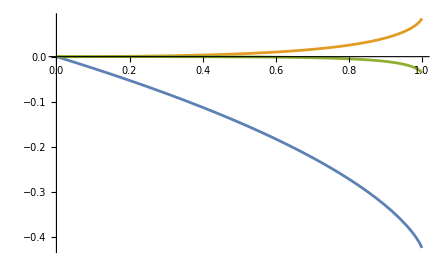

```mathematica
Plot[{(2 (70 (-2+T) T^2 EllipticE[T]-140 (-1+T) T^2 EllipticK[T]))/(105 π T^3),(2 (14 T (16+(-16+T) T) EllipticE[T]-112 (-2+T) (-1+T) T EllipticK[T]))/(105 π T^3), 1/(105 π T^3)2 (2 (-2+T) (128+T (-128+3 T)) EllipticE[T]-4 (-1+T) (128+T (-128+27 T)) EllipticK[T])},{T,0.0001,1}]
```

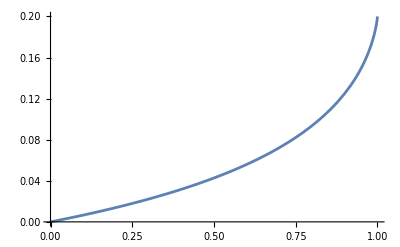

```mathematica
Plot[{-((2 (14 T (16+(-16+T) T) EllipticE[T]-112 (-2+T) (-1+T) T EllipticK[T]))/(105 π T^3)) / ((2 (70 (-2+T) T^2 EllipticE[T]-140 (-1+T) T^2 EllipticK[T]))/(105 π T^3))},{T,0.0001,1}]
```

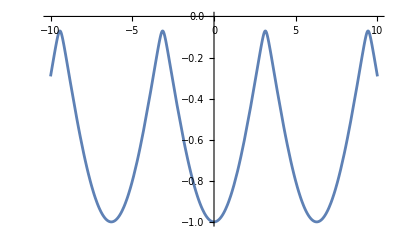

```mathematica
Plot[-√(1-0.995*Sin[x/2]^2),{x,-10,10}]
```

```mathematica
Manipulate[Plot[-(0.995* 10* Sin[x-y])/(2 √(4-2 0.995+2 0.995* Cos[x-y])),{x,-10,10} ],{y,-10,10}]
```